```mathematica
tovars[x_]:=Map[If[#<0,Subscript[b, -#](1-Subscript[a, -#]),Subscript[b, #](Subscript[a, #])]&,x]
tovar[x_]:=If[#<0,Subscript[b, -#](1-Subscript[a, -#]),Subscript[b, #](Subscript[a, #])]&[x]
tolist[x_]:=Table[x[[i]],{i,1,Length[x]}]
total2[x_]:=Piecewise[{{Total[x], ListQ[x]}, {x, True}}]
splitform[x_]:=Block[{list=tolist[x]},{Total[Map[If[NumberQ[#],#,If[NumberQ[First[#]],If[First[#]>0,#,0],#]]&,list]],-Total[Map[If[NumberQ[#],0,If[NumberQ[First[#]],If[First[#]>0,0,#],0]]&,list]]}]
```

```mathematica
pairswlen[list_,len_]:=Table[{list[[i]],list[[i+1]]},{i,1,len-1}]
pairs[list_]:=pairswlen[list,Length[list]]
```

```mathematica
path2form[path_]:=Times@@Map[If[#>0,Subscript[a, #] Subscript[b, #],(1-Subscript[a, -1*#])Subscript[b, -1*#]]&,Map[npairnum,pairs[path]]]
```

```mathematica
{Expand[Total[Map[path2form,FindPath[CompleteGraph[5],1,2,{1},All]]]],Expand[Total[Map[path2form,FindPath[CompleteGraph[5],2,1,∞,All]]]]}
%[[2]]-%[[1]]
FullSimplify[%]
splitform[Expand[%]]
Table[FullSimplify[-%[[1]][[i]]+%[[2]][[i]]],{i,1,Length[First[%]]}]//Column
(*Transpose[{Sort[tolist[Last[splitform[Expand[%]]]]],Sort[tolist[First[splitform[Expand[%]]]]]}]//TableForm*)
```

{a_1 b_1,b_1-a_1 b_1+a_3 b_2 b_3-a_2 a_3 b_2 b_3+a_5 b_4 b_5-a_4 a_5 b_4 b_5+a_3 a_6 b_3 b_4 b_6-a_3 a_4 a_6 b_3 b_4 b_6+a_5 b_2 b_5 b_6-a_2 a_5 b_2 b_5 b_6-a_5 a_6 b_2 b_5 b_6+a_2 a_5 a_6 b_2 b_5 b_6+a_8 b_7 b_8-a_7 a_8 b_7 b_8+a_3 a_9 b_3 b_7 b_9-a_3 a_7 a_9 b_3 b_7 b_9+a_5 a_9 b_5 b_6 b_7 b_9-a_5 a_6 a_9 b_5 b_6 b_7 b_9-a_5 a_7 a_9 b_5 b_6 b_7 b_9+a_5 a_6 a_7 a_9 b_5 b_6 b_7 b_9+a_8 b_2 b_8 b_9-a_2 a_8 b_2 b_8 b_9-a_8 a_9 b_2 b_8 b_9+a_2 a_8 a_9 b_2 b_8 b_9+a_6 a_8 b_4 b_6 b_8 b_9-a_4 a_6 a_8 b_4 b_6 b_8 b_9-a_6 a_8 a_9 b_4 b_6 b_8 b_9+a_4 a_6 a_8 a_9 b_4 b_6 b_8 b_9+a_5 a_10 b_5 b_7 b_10-a_5 a_7 a_10 b_5 b_7 b_10+a_3 a_6 a_10 b_3 b_6 b_7 b_10-a_3 a_6 a_7 a_10 b_3 b_6 b_7 b_10+a_8 b_4 b_8 b_10-a_4 a_8 b_4 b_8 b_10-a_8 a_10 b_4 b_8 b_10+a_4 a_8 a_10 b_4 b_8 b_10+a_8 b_2 b_6 b_8 b_10-a_2 a_8 b_2 b_6 b_8 b_10-a_6 a_8 b_2 b_6 b_8 b_10+a_2 a_6 a_8 b_2 b_6 b_8 b_10-a_8 a_10 b_2 b_6 b_8 b_10+a_2 a_8 a_10 b_2 b_6 b_8 b_10+a_6 a_8 a_10 b_2 b_6 b_8 b_10-a_2 a_6 a_8 a_10 b_2 b_6 b_8 b_10+a_3 a_9 b_3 b_4 b_9 b_10-a_3 a_4 a_9 b_3 b_4 b_9 b_10-a_3 a_9 a_10 b_3 b_4 b_9 b_10+a_3 a_4 a_9 a_10 b_3 b_4 b_9 b_10+a_5 a_10 b_2 b_5 b_9 b_10-a_2 a_5 a_10 b_2 b_5 b_9 b_10-a_5 a_9 a_10 b_2 b_5 b_9 b_10+a_2 a_5 a_9 a_10 b_2 b_5 b_9 b_10}

b_1-2 a_1 b_1+a_3 b_2 b_3-a_2 a_3 b_2 b_3+a_5 b_4 b_5-a_4 a_5 b_4 b_5+a_3 a_6 b_3 b_4 b_6-a_3 a_4 a_6 b_3 b_4 b_6+a_5 b_2 b_5 b_6-a_2 a_5 b_2 b_5 b_6-a_5 a_6 b_2 b_5 b_6+a_2 a_5 a_6 b_2 b_5 b_6+a_8 b_7 b_8-a_7 a_8 b_7 b_8+a_3 a_9 b_3 b_7 b_9-a_3 a_7 a_9 b_3 b_7 b_9+a_5 a_9 b_5 b_6 b_7 b_9-a_5 a_6 a_9 b_5 b_6 b_7 b_9-a_5 a_7 a_9 b_5 b_6 b_7 b_9+a_5 a_6 a_7 a_9 b_5 b_6 b_7 b_9+a_8 b_2 b_8 b_9-a_2 a_8 b_2 b_8 b_9-a_8 a_9 b_2 b_8 b_9+a_2 a_8 a_9 b_2 b_8 b_9+a_6 a_8 b_4 b_6 b_8 b_9-a_4 a_6 a_8 b_4 b_6 b_8 b_9-a_6 a_8 a_9 b_4 b_6 b_8 b_9+a_4 a_6 a_8 a_9 b_4 b_6 b_8 b_9+a_5 a_10 b_5 b_7 b_10-a_5 a_7 a_10 b_5 b_7 b_10+a_3 a_6 a_10 b_3 b_6 b_7 b_10-a_3 a_6 a_7 a_10 b_3 b_6 b_7 b_10+a_8 b_4 b_8 b_10-a_4 a_8 b_4 b_8 b_10-a_8 a_10 b_4 b_8 b_10+a_4 a_8 a_10 b_4 b_8 b_10+a_8 b_2 b_6 b_8 b_10-a_2 a_8 b_2 b_6 b_8 b_10-a_6 a_8 b_2 b_6 b_8 b_10+a_2 a_6 a_8 b_2 b_6 b_8 b_10-a_8 a_10 b_2 b_6 b_8 b_10+a_2 a_8 a_10 b_2 b_6 b_8 b_10+a_6 a_8 a_10 b_2 b_6 b_8 b_10-a_2 a_6 a_8 a_10 b_2 b_6 b_8 b_10+a_3 a_9 b_3 b_4 b_9 b_10-a_3 a_4 a_9 b_3 b_4 b_9 b_10-a_3 a_9 a_10 b_3 b_4 b_9 b_10+a_3 a_4 a_9 a_10 b_3 b_4 b_9 b_10+a_5 a_10 b_2 b_5 b_9 b_10-a_2 a_5 a_10 b_2 b_5 b_9 b_10-a_5 a_9 a_10 b_2 b_5 b_9 b_10+a_2 a_5 a_9 a_10 b_2 b_5 b_9 b_10

(1-2 a_1) b_1+a_8 b_8 (-(-1+a_7) b_7+(-1+a_9) ((-1+a_2) b_2+(-1+a_4) a_6 b_4 b_6) b_9+(-1+a_10) ((-1+a_4) b_4-(-1+a_2) (-1+a_6) b_2 b_6) b_10)+a_3 b_3 (-(-1+a_2) b_2+a_9 b_9 (-(-1+a_7) b_7+(-1+a_4) (-1+a_10) b_4 b_10)+a_6 b_6 (-(-1+a_4) b_4-(-1+a_7) a_10 b_7 b_10))+a_5 b_5 (-(-1+a_4) b_4+(-1+a_7) b_7 ((-1+a_6) a_9 b_6 b_9-a_10 b_10)+(-1+a_2) b_2 ((-1+a_6) b_6+(-1+a_9) a_10 b_9 b_10))

{b_1+a_3 b_2 b_3+a_5 b_4 b_5+a_3 a_6 b_3 b_4 b_6+a_5 b_2 b_5 b_6+a_2 a_5 a_6 b_2 b_5 b_6+a_8 b_7 b_8+a_3 a_9 b_3 b_7 b_9+a_5 a_9 b_5 b_6 b_7 b_9+a_5 a_6 a_7 a_9 b_5 b_6 b_7 b_9+a_8 b_2 b_8 b_9+a_2 a_8 a_9 b_2 b_8 b_9+a_6 a_8 b_4 b_6 b_8 b_9+a_4 a_6 a_8 a_9 b_4 b_6 b_8 b_9+a_5 a_10 b_5 b_7 b_10+a_3 a_6 a_10 b_3 b_6 b_7 b_10+a_8 b_4 b_8 b_10+a_4 a_8 a_10 b_4 b_8 b_10+a_8 b_2 b_6 b_8 b_10+a_2 a_6 a_8 b_2 b_6 b_8 b_10+a_2 a_8 a_10 b_2 b_6 b_8 b_10+a_6 a_8 a_10 b_2 b_6 b_8 b_10+a_3 a_9 b_3 b_4 b_9 b_10+a_3 a_4 a_9 a_10 b_3 b_4 b_9 b_10+a_5 a_10 b_2 b_5 b_9 b_10+a_2 a_5 a_9 a_10 b_2 b_5 b_9 b_10,2 a_1 b_1+a_2 a_3 b_2 b_3+a_4 a_5 b_4 b_5+a_3 a_4 a_6 b_3 b_4 b_6+a_2 a_5 b_2 b_5 b_6+a_5 a_6 b_2 b_5 b_6+a_7 a_8 b_7 b_8+a_3 a_7 a_9 b_3 b_7 b_9+a_5 a_6 a_9 b_5 b_6 b_7 b_9+a_5 a_7 a_9 b_5 b_6 b_7 b_9+a_2 a_8 b_2 b_8 b_9+a_8 a_9 b_2 b_8 b_9+a_4 a_6 a_8 b_4 b_6 b_8 b_9+a_6 a_8 a_9 b_4 b_6 b_8 b_9+a_5 a_7 a_10 b_5 b_7 b_10+a_3 a_6 a_7 a_10 b_3 b_6 b_7 b_10+a_4 a_8 b_4 b_8 b_10+a_8 a_10 b_4 b_8 b_10+a_2 a_8 b_2 b_6 b_8 b_10+a_6 a_8 b_2 b_6 b_8 b_10+a_8 a_10 b_2 b_6 b_8 b_10+a_2 a_6 a_8 a_10 b_2 b_6 b_8 b_10+a_3 a_4 a_9 b_3 b_4 b_9 b_10+a_3 a_9 a_10 b_3 b_4 b_9 b_10+a_2 a_5 a_10 b_2 b_5 b_9 b_10+a_5 a_9 a_10 b_2 b_5 b_9 b_10}

(-1+2 a_1) b_1
(-1+a_2) a_3 b_2 b_3
(-1+a_4) a_5 b_4 b_5
a_3 (-1+a_4) a_6 b_3 b_4 b_6
(-1+a_2) a_5 b_2 b_5 b_6
-(-1+a_2) a_5 a_6 b_2 b_5 b_6
(-1+a_7) a_8 b_7 b_8
a_3 (-1+a_7) a_9 b_3 b_7 b_9
a_5 (-1+a_6) a_9 b_5 b_6 b_7 b_9
-a_5 (-1+a_6) a_7 a_9 b_5 b_6 b_7 b_9
(-1+a_2) a_8 b_2 b_8 b_9
-(-1+a_2) a_8 a_9 b_2 b_8 b_9
(-1+a_4) a_6 a_8 b_4 b_6 b_8 b_9
-(-1+a_4) a_6 a_8 a_9 b_4 b_6 b_8 b_9
a_5 (-1+a_7) a_10 b_5 b_7 b_10
a_3 a_6 (-1+a_7) a_10 b_3 b_6 b_7 b_10
(-1+a_4) a_8 b_4 b_8 b_10
-(-1+a_4) a_8 a_10 b_4 b_8 b_10
(-1+a_2) a_8 b_2 b_6 b_8 b_10
-(-1+a_2) a_6 a_8 b_2 b_6 b_8 b_10
-(-1+a_2) a_8 a_10 b_2 b_6 b_8 b_10
(-1+a_2) a_6 a_8 a_10 b_2 b_6 b_8 b_10
a_3 (-1+a_4) a_9 b_3 b_4 b_9 b_10
-a_3 (-1+a_4) a_9 a_10 b_3 b_4 b_9 b_10
(-1+a_2) a_5 a_10 b_2 b_5 b_9 b_10
-(-1+a_2) a_5 a_9 a_10 b_2 b_5 b_9 b_10

```mathematica
(-1+Subscript[a, 1]) (Subscript[b, 1])
(-1+Subscript[a, 2])(+Subscript[a, 3] Subscript[b, 2] Subscript[b, 3]+ Subscript[a, 5] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6]- Subscript[a, 5] Subscript[a, 6] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6])
(-1+Subscript[a, 3])(- Subscript[a, 7] Subscript[b, 3] Subscript[b, 6] Subscript[b, 7] Subscript[b, 10]+ Subscript[a, 6] Subscript[a, 7] Subscript[b, 3] Subscript[b, 6] Subscript[b, 7] Subscript[b, 10]+ Subscript[a, 7] Subscript[a, 10] Subscript[b, 3] Subscript[b, 6] Subscript[b, 7] Subscript[b, 10]- Subscript[a, 6] Subscript[a, 7] Subscript[a, 10] Subscript[b, 3] Subscript[b, 6] Subscript[b, 7] Subscript[b, 10]- Subscript[a, 7] Subscript[b, 3] Subscript[b, 6] Subscript[b, 7] Subscript[b, 10]+ Subscript[a, 6] Subscript[a, 7] Subscript[b, 3] Subscript[b, 6] Subscript[b, 7] Subscript[b, 10]+ Subscript[a, 7] Subscript[a, 10] Subscript[b, 3] Subscript[b, 6] Subscript[b, 7] Subscript[b, 10]- Subscript[a, 6] Subscript[a, 7] Subscript[a, 10] Subscript[b, 3] Subscript[b, 6] Subscript[b, 7] Subscript[b, 10]- Subscript[a, 4] Subscript[a, 10] Subscript[b, 3] Subscript[b, 4] Subscript[b, 9] Subscript[b, 10]+ Subscript[a, 4] Subscript[a, 9] Subscript[a, 10] Subscript[b, 3] Subscript[b, 4] Subscript[b, 9] Subscript[b, 10])
(-1+Subscript[a, 4])(+Subscript[a, 5] Subscript[b, 4] Subscript[b, 5]+Subscript[a, 3] Subscript[a, 6] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6])
(-1+Subscript[a, 5])(-Subscript[a, 2] Subscript[a, 9] Subscript[b, 2] Subscript[b, 5] Subscript[b, 9] Subscript[b, 10]+Subscript[a, 2] Subscript[a, 9] Subscript[a, 10] Subscript[b, 2] Subscript[b, 5] Subscript[b, 9] Subscript[b, 10]-Subscript[a, 6] Subscript[a, 7] Subscript[b, 5] Subscript[b, 6] Subscript[b, 7] Subscript[b, 9]+Subscript[a, 6] Subscript[a, 7] Subscript[a, 9] Subscript[b, 5] Subscript[b, 6] Subscript[b, 7] Subscript[b, 9])
(-1+Subscript[a, 6])(-Subscript[a, 4] Subscript[a, 9] Subscript[b, 4] Subscript[b, 6] Subscript[b, 8] Subscript[b, 9]+Subscript[a, 4] Subscript[a, 8] Subscript[a, 9] Subscript[b, 4] Subscript[b, 6] Subscript[b, 8] Subscript[b, 9])
(-1+Subscript[a, 8])(-Subscript[a, 2] Subscript[a, 6] Subscript[a, 10] Subscript[b, 2] Subscript[b, 6] Subscript[b, 8] Subscript[b, 10])
```

```mathematica
Reduce[{Subscript[b, 1]-2 Subscript[a, 1] Subscript[b, 1]-Subscript[a, 2] Subscript[b, 2] Subscript[b, 3]+Subscript[a, 3] Subscript[b, 2] Subscript[b, 3]-Subscript[a, 4] Subscript[b, 4] Subscript[b, 5]+Subscript[a, 5] Subscript[b, 4] Subscript[b, 5]-Subscript[a, 4] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]+Subscript[a, 3] Subscript[a, 4] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]+Subscript[a, 3] Subscript[a, 6] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]+Subscript[a, 4] Subscript[a, 6] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]-2 Subscript[a, 3] Subscript[a, 4] Subscript[a, 6] Subscript[b, 3] Subscript[b, 4] Subscript[b, 6]+Subscript[a, 5] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6]-Subscript[a, 2] Subscript[a, 5] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6]-Subscript[a, 2] Subscript[a, 6] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6]-Subscript[a, 5] Subscript[a, 6] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6]+2 Subscript[a, 2] Subscript[a, 5] Subscript[a, 6] Subscript[b, 2] Subscript[b, 5] Subscript[b, 6]<0,0≤Subscript[b, 1]≤1,0≤Subscript[b, 2]≤1,0≤Subscript[b, 3]≤1,0≤Subscript[b, 4]≤1,0≤Subscript[b, 5]≤1,0≤Subscript[b, 6]≤1,0≤Subscript[a, 1]≤1,0≤Subscript[a, 2]≤1,0≤Subscript[a, 3]≤1,0≤Subscript[a, 4]≤1,0≤Subscript[a, 5]≤1,0≤Subscript[a, 6]≤1},Integers]
```

```mathematica
Table[Length[tolist[Expand[Total[Map[path2form,FindPath[CompleteGraph[l],1,2,∞,All]]]]]],{l,3,7}]
```

{3,11,51,299,2163}

```mathematica
npairnum[{i_,j_}]:=If[i<j,(1+i+1/2 (-3+j) j),If[i>j,-(1+j+1/2 (-3+i) i),0]]
npair[n_]:={n-Binomial[Floor[(1+Sqrt[8*n])/2],2],Floor[Sqrt[2*(n)]+1/2]+1}
Table[npair[i],{i,1,10}]
```

{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}}

```mathematica
Table[2+npair[i],{i,1,10}]
```

{{3,4},{3,5},{4,5},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7},{6,7}}

```mathematica
1,a,2
1,a,b,2
1,a,x,b,2
```

```mathematica
Table[{npairnum[{1,i}],npairnum[{i,2}]},{i,3,10}]
InterpolatingPolynomial[Map[First,%],i]
```

{{2,-3},{4,-5},{7,-8},{11,-12},{16,-17},{22,-23},{29,-30},{37,-38}}

2+(2+1/2 (-2+i)) (-1+i)

```mathematica
Table[{npairnum[{1,3}],npairnum[{j,2}]},{j,4,15}]
InterpolatingPolynomial[-Map[Last,%],j]
```

{{2,-5},{2,-8},{2,-12},{2,-17},{2,-23},{2,-30},{2,-38},{2,-47},{2,-57},{2,-68},{2,-80},{2,-93}}

5+(3+1/2 (-2+j)) (-1+j)

```mathematica
Table[{npairnum[{1,4}],npairnum[{j,2}]},{j,3,3}]
Table[{npairnum[{1,4}],npairnum[{j,2}]},{j,5,15}]
InterpolatingPolynomial[-Map[Last,%],j]
```

{{4,-3}}

{{4,-8},{4,-12},{4,-17},{4,-23},{4,-30},{4,-38},{4,-47},{4,-57},{4,-68},{4,-80},{4,-93}}

8+(4+1/2 (-2+j)) (-1+j)

```mathematica
Table[{npairnum[{1,5}],npairnum[{j,2}]},{j,3,4}]
Table[{npairnum[{1,5}],npairnum[{j,2}]},{j,6,15}]
InterpolatingPolynomial[-Map[Last,%],j]
```

{{7,-3},{7,-5}}

{{7,-12},{7,-17},{7,-23},{7,-30},{7,-38},{7,-47},{7,-57},{7,-68},{7,-80},{7,-93}}

12+(5+1/2 (-2+j)) (-1+j)

```mathematica
Table[{npairnum[{1,6}],npairnum[{j,2}]},{j,3,5}]
Table[{npairnum[{1,6}],npairnum[{j,2}]},{j,7,15}]
InterpolatingPolynomial[-Map[Last,%],j]
```

{{11,-3},{11,-5},{11,-8}}

{{11,-17},{11,-23},{11,-30},{11,-38},{11,-47},{11,-57},{11,-68},{11,-80},{11,-93}}

17+(6+1/2 (-2+j)) (-1+j)

```mathematica
Table[{npairnum[{1,7}],npairnum[{j,2}]},{j,3,6}]
Table[{npairnum[{1,7}],npairnum[{j,2}]},{j,8,15}]
InterpolatingPolynomial[-Map[Last,%],j]
```

{{16,-3},{16,-5},{16,-8},{16,-12}}

{{16,-23},{16,-30},{16,-38},{16,-47},{16,-57},{16,-68},{16,-80},{16,-93}}

23+(7+1/2 (-2+j)) (-1+j)

```mathematica
Table[{npairnum[{1,8}],npairnum[{j,2}]},{j,3,7}]
Table[{npairnum[{1,8}],npairnum[{j,2}]},{j,9,17}]
InterpolatingPolynomial[-Map[Last,%],j]
```

{{22,-3},{22,-5},{22,-8},{22,-12},{22,-17}}

{{22,-30},{22,-38},{22,-47},{22,-57},{22,-68},{22,-80},{22,-93},{22,-107},{22,-122}}

30+(8+1/2 (-2+j)) (-1+j)

```mathematica
Table[{npairnum[{1,9}],npairnum[{j,2}]},{j,3,8}]
Table[{npairnum[{1,9}],npairnum[{j,2}]},{j,10,19}]
InterpolatingPolynomial[-Map[Last,%],j]
```

{{29,-3},{29,-5},{29,-8},{29,-12},{29,-17},{29,-23}}

{{29,-38},{29,-47},{29,-57},{29,-68},{29,-80},{29,-93},{29,-107},{29,-122},{29,-138},{29,-155}}

38+(9+1/2 (-2+j)) (-1+j)

```mathematica
InterpolatingPolynomial[{{3,2},{4,4},{5,7},{6,11},{7,16},{8,22},{9,29}},i]
```

2+(2+1/2 (-4+i)) (-3+i)

```mathematica
InterpolatingPolynomial[{{3,5},{4,8},{5,12},{6,17},{7,23},{8,30},{9,38}},i]
```

5+(3+1/2 (-4+i)) (-3+i)

```mathematica
(*i>j*){i,j}->{1/2 (4+(-3+i) i),-3+(-2+(4-j)/2) (-3+j)}
(*i<j*){i,j}->{2+(2+1/2 (-4+i)) (-3+i),-((5+(3+1/2 (-4+i)) (-3+i))+(j+1/2(j-2))(j-1))}=={1/2 (4+(-3+i) i),-1/2 (6+(-1+i) i+j (-5+3 j))}
```

```mathematica
InterpolatingPolynomial[{{3,-3},{4,-5},{5,-8},{6,-12},{7,-17},{8,-23}},j]
```

-3+(-2+(4-j)/2) (-3+j)

```mathematica
{1,i,2}->{1/2 (2+i+i^2),1/2 (-4-i (1+i))}
{1,i,j,2}->{1/2 (4+(-3+i) i),-3+(-2+(4-j)/2) (-3+j)}{j,3,i-1}∪{1/2 (4+(-3+i) i),-1/2 (6+(-1+i) i+j (-5+3 j))}{j,i+1,nn}
{1,i,x,j,2}

{2,i,1}->-{1/2 (2+i+i^2),1/2 (-4-i (1+i))}
{1,i,j,2}->-{1/2 (4+(-3+i) i),-3+(-2+(4-j)/2) (-3+j)}{j,3,i-1}∪{1/2 (4+(-3+i) i),-1/2 (6+(-1+i) i+j (-5+3 j))}{j,i+1,nn}
{1,i,x,j,2}->{-{1,i},¬x,-{j,2}}
```

```mathematica
Table[FullSimplify[(Subscript[a, 1/2 (2+i+i^2)]*Subscript[b, 1/2 (2+i+i^2)]*(1-Subscript[a, -1/2 (-4-i (1+i))])Subscript[b, -1/2 (-4-i (1+i))])-((1-Subscript[a, 1/2 (2+i+i^2)])*Subscript[b, 1/2 (2+i+i^2)]*Subscript[a, -1/2 (-4-i (1+i))] Subscript[b, -1/2 (-4-i (1+i))])],{i,1,10}]
```

{(a_2-a_3) b_2 b_3,(a_4-a_5) b_4 b_5,(a_7-a_8) b_7 b_8,(a_11-a_12) b_11 b_12,(a_16-a_17) b_16 b_17,(a_22-a_23) b_22 b_23,(a_29-a_30) b_29 b_30,(a_37-a_38) b_37 b_38,(a_46-a_47) b_46 b_47,(a_56-a_57) b_56 b_57}

```mathematica
Table[Sum[FullSimplify[(Subscript[a, 1/2 (4+(-3+i) i)])Subscript[b, 1/2 (4+(-3+i) i)]*(1-Subscript[a, 1/2 (6+(-3+j) j)])Subscript[b, 1/2 (6+(-3+j) j)]-(1-Subscript[a, 1/2 (4+(-3+i) i)])Subscript[b, 1/2 (4+(-3+i) i)]*(Subscript[a, 1/2 (6+(-3+j) j)])Subscript[b, 1/2 (6+(-3+j) j)]],{j,3,i-1}],{i,4,8}]//Column
Table[Sum[FullSimplify[(Subscript[a, 1/2 (4+(-3+i) i)])Subscript[b, 1/2 (4+(-3+i) i)]*(1-Subscript[a, 1/2 (6+(-1+i) i+j (-5+3 j))])Subscript[b, 1/2 (6+(-1+i) i+j (-5+3 j))]-(1-Subscript[a, 1/2 (4+(-3+i) i)])Subscript[b, 1/2 (4+(-3+i) i)]*(Subscript[a, 1/2 (6+(-1+i) i+j (-5+3 j))])Subscript[b, 1/2 (6+(-1+i) i+j (-5+3 j))]],{j,i+1,15}],{i,4,8}]
```

(-a_3+a_4) b_3 b_4
(-a_3+a_7) b_3 b_7+(-a_5+a_7) b_5 b_7
(-a_3+a_11) b_3 b_11+(-a_5+a_11) b_5 b_11+(-a_8+a_11) b_8 b_11
(-a_3+a_16) b_3 b_16+(-a_5+a_16) b_5 b_16+(-a_8+a_16) b_8 b_16+(-a_12+a_16) b_12 b_16
(-a_3+a_22) b_3 b_22+(-a_5+a_22) b_5 b_22+(-a_8+a_22) b_8 b_22+(-a_12+a_22) b_12 b_22+(-a_17+a_22) b_17 b_22

{(a_4-a_34) b_4 b_34+(a_4-a_48) b_4 b_48+(a_4-a_65) b_4 b_65+(a_4-a_85) b_4 b_85+(a_4-a_108) b_4 b_108+(a_4-a_134) b_4 b_134+(a_4-a_163) b_4 b_163+(a_4-a_195) b_4 b_195+(a_4-a_230) b_4 b_230+(a_4-a_268) b_4 b_268+(a_4-a_309) b_4 b_309,(a_7-a_52) b_7 b_52+(a_7-a_69) b_7 b_69+(a_7-a_89) b_7 b_89+(a_7-a_112) b_7 b_112+(a_7-a_138) b_7 b_138+(a_7-a_167) b_7 b_167+(a_7-a_199) b_7 b_199+(a_7-a_234) b_7 b_234+(a_7-a_272) b_7 b_272+(a_7-a_313) b_7 b_313,(a_11-a_74) b_11 b_74+(a_11-a_94) b_11 b_94+(a_11-a_117) b_11 b_117+(a_11-a_143) b_11 b_143+(a_11-a_172) b_11 b_172+(a_11-a_204) b_11 b_204+(a_11-a_239) b_11 b_239+(a_11-a_277) b_11 b_277+(a_11-a_318) b_11 b_318,(a_16-a_100) b_16 b_100+(a_16-a_123) b_16 b_123+(a_16-a_149) b_16 b_149+(a_16-a_178) b_16 b_178+(a_16-a_210) b_16 b_210+(a_16-a_245) b_16 b_245+(a_16-a_283) b_16 b_283+(a_16-a_324) b_16 b_324,(a_22-a_130) b_22 b_130+(a_22-a_156) b_22 b_156+(a_22-a_185) b_22 b_185+(a_22-a_217) b_22 b_217+(a_22-a_252) b_22 b_252+(a_22-a_290) b_22 b_290+(a_22-a_331) b_22 b_331}

```mathematica
FullSimplify[-1*(-1/2 (6+(-1+i) i+j (-5+3 j)))]
```

1/2 (6+(-1+i) i+j (-5+3 j))

```mathematica
1,2
1,3
2,3
1,2,3
1,4
2,4
3,4
1,2,4
1,3,4
2,3,4
1,2,3,4
1,5
2,5
3,5
4,5
1,2,5
1,3,5
1,4,5
2,3,5
2,4,5
3,4,5
1,2,3,5
1,2,4,5
1,3,4,5
2,3,4,5
1,2,3,4,5
1,6
2,6
3,6
4,6
5,6
1,2,6
1,3,6
1,4,6
1,5,6
2,3,6
2,4,6
2,5,6
3,4,6
3,5,6
4,5,6
1,2,3,6
1,2,4,6
1,2,5,6
2,3,4,6
2,3,5,6
3,4,5,6
1,2,3,4,6
1,2,3,5,6
1,2,4,5,6
1,3,4,5,6
2,3,4,5,6
1,2,3,4,5,6
1,7
2,7
3,7
4,7
5,7
6,7
1,2,7
1,3,7
1,4,7
1,5,7
1,6,7
2,3,7
2,4,7
2,5,7
2,6,7
3,4,7
3,5,7
3,6,7
4,5,7
4,6,7
5,6,7
1,2,3,7
1,2,4,7
1,2,5,7
1,2,6,7
1,3,6,7
1,4,5,7
1,4,6,7
1,5,6,7
2,3,4,7
2,3,5,7
2,3,6,7
2,4,5,7
2,4,6,7
2,5,6,7
3,4,5,7
3,4,6,7
4,5,6,7
1,2,3,4,7
1,2,3,5,7
1,2,3,6,7
1,2,4,5,7
1,2,4,6,7
1,2,5,6,7
2,3,4,5,7
2,3,4,6,7
2,3,5,6,7
2,4,5,6,7
3,4,5,6,7
1,2,3,4,5,7
1,2,3,4,6,7
1,2,3,5,6,7
1,2,4,5,6,7
1,3,4,5,6,7
2,3,4,5,6,7
1,2,3,4,5,6,7
```

```mathematica
rtups={{1,2},
{1,3},
{2,3},
{1,2,3},
{1,4},
{2,4},
{3,4},
{1,2,4},
{1,3,4},
{2,3,4},
{1,2,3,4},
{1,5},
{2,5},
{3,5},
{4,5},
{1,2,5},
{1,3,5},
{1,4,5},
{2,3,5},
{2,4,5},
{3,4,5},
{1,2,3,5},
{1,2,4,5},
{1,3,4,5},
{2,3,4,5},
{1,2,3,4,5},
{1,6},
{2,6},
{3,6},
{4,6},
{5,6},
{1,2,6},
{1,3,6},
{1,4,6},
{1,5,6},
{2,3,6},
{2,4,6},
{2,5,6},
{3,4,6},
{3,5,6},
{4,5,6},
{1,2,3,6},
{1,2,4,6},
{1,2,5,6},
{2,3,4,6},
{2,3,5,6},
{3,4,5,6},
{1,2,3,4,6},
{1,2,3,5,6},
{1,2,4,5,6},
{1,3,4,5,6},
{2,3,4,5,6},
{1,2,3,4,5,6},
{1,7},
{2,7},
{3,7},
{4,7},
{5,7},
{6,7},
{1,2,7},
{1,3,7},
{1,4,7},
{1,5,7},
{1,6,7},
{2,3,7},
{2,4,7},
{2,5,7},
{2,6,7},
{3,4,7},
{3,5,7},
{3,6,7},
{4,5,7},
{4,6,7},
{5,6,7},
{1,2,3,7},
{1,2,4,7},
{1,2,5,7},
{1,2,6,7},
{1,3,6,7},
{1,4,5,7},
{1,4,6,7},
{1,5,6,7},
{2,3,4,7},
{2,3,5,7},
{2,3,6,7},
{2,4,5,7},
{2,4,6,7},
{2,5,6,7},
{3,4,5,7},
{3,4,6,7},
{4,5,6,7},
{1,2,3,4,7},
{1,2,3,5,7},
{1,2,3,6,7},
{1,2,4,5,7},
{1,2,4,6,7},
{1,2,5,6,7},
{2,3,4,5,7},
{2,3,4,6,7},
{2,3,5,6,7},
{2,4,5,6,7},
{3,4,5,6,7},
{1,2,3,4,5,7},
{1,2,3,4,6,7},
{1,2,3,5,6,7},
{1,2,4,5,6,7},
{1,3,4,5,6,7},
{2,3,4,5,6,7},
{1,2,3,4,5,6,7}};
```

```mathematica
"This is the sequence of subsets of increasing elements such that the next element only has greater length if all possible combinations of lesser length and equal/lesster value have been exhausted, and only has a greater element if all increasing combinations of lesser elements have been exhausted.";
```

```mathematica
Map[First,Map[Reverse,rtups]]
Tally[%]
Flatten[Table[First[Position[%,i]],{i,2,7}]]
```

{2,3,3,3,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7}

{{2,1},{3,3},{4,7},{5,15},{6,27},{7,56}}

{1,1,2,1,3,1,4,1,5,1,3,2}

```mathematica
Expand[InterpolatingPolynomial[{1,3,7,15,27,56},f]]
```

-18+(493 f)/12-(769 f^2)/24+(283 f^3)/24-(47 f^4)/24+f^5/8

```mathematica
filledfromto[l_,s_,f_]:=And@@Table[l[[i]]-1==l[[i+1]],{i,s,f-1}]
nexttup[l_]:=
If[First[l]==Length[l],{l[[1]]+1,1},
If[filledfromto[l,1,Length[l]],Append[l,Last[l]-1],
If[Length[l]==2,{l[[1]],l[[2]]+1},
Join[{l[[1]]},nexttup[Drop[l,1]]]]]]
```

```mathematica
nexttup[{2,1}]
nexttup[{3,2,1}]
nexttup[%]
```

{3,1}

{4,1}

{4,2}

```mathematica
NestList[nexttup,{2,1},30]//Column
```

```mathematica
Map[#&,rtups]//Column
```

{1,2}
{1,3}
{2,3}
{1,2,3}
{1,4}
{2,4}
{3,4}
{1,2,4}
{1,3,4}
{2,3,4}
{1,2,3,4}
{1,5}
{2,5}
{3,5}
{4,5}
{1,2,5}
{1,3,5}
{1,4,5}
{2,3,5}
{2,4,5}
{3,4,5}
{1,2,3,5}
{1,2,4,5}
{1,3,4,5}
{2,3,4,5}
{1,2,3,4,5}
{1,6}
{2,6}
{3,6}
{4,6}
{5,6}
{1,2,6}
{1,3,6}
{1,4,6}
{1,5,6}
{2,3,6}
{2,4,6}
{2,5,6}
{3,4,6}
{3,5,6}
{4,5,6}
{1,2,3,6}
{1,2,4,6}
{1,2,5,6}
{2,3,4,6}
{2,3,5,6}
{3,4,5,6}
{1,2,3,4,6}
{1,2,3,5,6}
{1,2,4,5,6}
{1,3,4,5,6}
{2,3,4,5,6}
{1,2,3,4,5,6}
{1,7}
{2,7}
{3,7}
{4,7}
{5,7}
{6,7}
{1,2,7}
{1,3,7}
{1,4,7}
{1,5,7}
{1,6,7}
{2,3,7}
{2,4,7}
{2,5,7}
{2,6,7}
{3,4,7}
{3,5,7}
{3,6,7}
{4,5,7}
{4,6,7}
{5,6,7}
{1,2,3,7}
{1,2,4,7}
{1,2,5,7}
{1,2,6,7}
{1,3,6,7}
{1,4,5,7}
{1,4,6,7}
{1,5,6,7}
{2,3,4,7}
{2,3,5,7}
{2,3,6,7}
{2,4,5,7}
{2,4,6,7}
{2,5,6,7}
{3,4,5,7}
{3,4,6,7}
{4,5,6,7}
{1,2,3,4,7}
{1,2,3,5,7}
{1,2,3,6,7}
{1,2,4,5,7}
{1,2,4,6,7}
{1,2,5,6,7}
{2,3,4,5,7}
{2,3,4,6,7}
{2,3,5,6,7}
{2,4,5,6,7}
{3,4,5,6,7}
{1,2,3,4,5,7}
{1,2,3,4,6,7}
{1,2,3,5,6,7}
{1,2,4,5,6,7}
{1,3,4,5,6,7}
{2,3,4,5,6,7}
{1,2,3,4,5,6,7}

```mathematica
{{2,-2+a+b},
{3,4+b+(-3/2-c/2) c+a (-4+a+c)},
{4,-4+b+(-3/2-c/2) c+(-6-d) d+a (14/3+(-2+a/3) a+c+2 d)}}//Expand
```

{{2,-2+a+b},{3,4-4 a+a^2+b-(3 c)/2+a c-c^2/2},{4,-4+(14 a)/3-2 a^2+a^3/3+b-(3 c)/2+a c-c^2/2-6 d+2 a d-d^2}}

```mathematica
InterpolatingPolynomial[{1,4,11,26,53,109},n]
```

1+(3+(2+(2/3+13/120 (-5+n) (-4+n)) (-3+n)) (-2+n)) (-1+n)

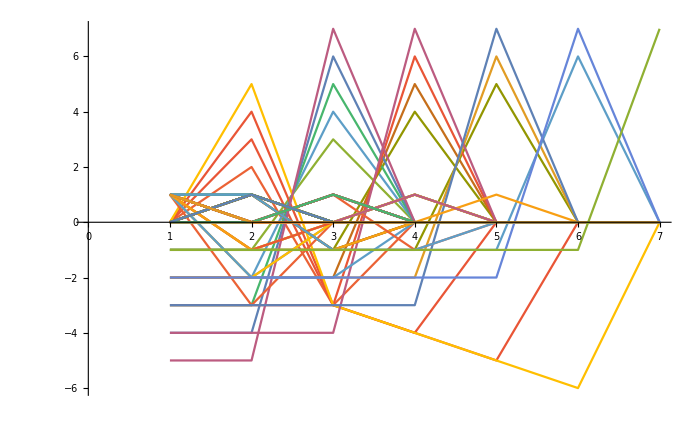

```mathematica
ListPlot[Differences[Map[PadRight[#,7]&,rtups]],Joined->True]
```

```mathematica
Map[Piecewise[{{0, #==0}, {1, #==1}, {2, #<0}}]&,Differences[Map[First,rtups]]]
```

{0,1,2,0,1,1,2,0,1,2,0,1,1,1,2,0,0,1,0,1,2,0,0,1,2,0,1,1,1,1,2,0,0,0,1,0,0,1,0,1,2,0,0,1,0,1,2,0,0,0,1,2,0,1,1,1,1,1,2,0,0,0,0,1,0,0,0,1,0,0,1,0,1,2,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,2,0,0,0,0,0,1,0,0,0,1,2,0,0,0,0,1,2}

```mathematica
ntuples[n_,m_]:=
Block[{(*m=2n,*)
is=Reverse[Table[Subscript[i, j],{j,1,n}]]},
Block[{lims=Reverse[Join[{{Subscript[i, 1],n,m}},Table[{Subscript[i, j],n+1-j,Subscript[i, j-1]-1},{j,2,n}]]]},
Block[{toout=Flatten[Fold[Table,is,lims],n-1]},toout]]]
```

```mathematica
Map[npairnums,ntuples[2,5]]
```

Table::iterb: Iterator {i_2, 1, -1 + i_1} does not have appropriate bounds.

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}

```mathematica
Map[npairnums,ntuples[3,10]]
```

Table::iterb: Iterator {i_3, 1, -1 + i_2} does not have appropriate bounds.

Table::iterb: Iterator {i_2, 2, -1 + i_1} does not have appropriate bounds.

{{1,3},{1,5},{2,6},{3,6},{1,8},{2,9},{3,9},{4,10},{5,10},{6,10},{1,12},{2,13},{3,13},{4,14},{5,14},{6,14},{7,15},{8,15},{9,15},{10,15},{1,17},{2,18},{3,18},{4,19},{5,19},{6,19},{7,20},{8,20},{9,20},{10,20},{11,21},{12,21},{13,21},{14,21},{15,21},{1,23},{2,24},{3,24},{4,25},{5,25},{6,25},{7,26},{8,26},{9,26},{10,26},{11,27},{12,27},{13,27},{14,27},{15,27},{16,28},{17,28},{18,28},{19,28},{20,28},{21,28},{1,30},{2,31},{3,31},{4,32},{5,32},{6,32},{7,33},{8,33},{9,33},{10,33},{11,34},{12,34},{13,34},{14,34},{15,34},{16,35},{17,35},{18,35},{19,35},{20,35},{21,35},{22,36},{23,36},{24,36},{25,36},{26,36},{27,36},{28,36},{1,38},{2,39},{3,39},{4,40},{5,40},{6,40},{7,41},{8,41},{9,41},{10,41},{11,42},{12,42},{13,42},{14,42},{15,42},{16,43},{17,43},{18,43},{19,43},{20,43},{21,43},{22,44},{23,44},{24,44},{25,44},{26,44},{27,44},{28,44},{29,45},{30,45},{31,45},{32,45},{33,45},{34,45},{35,45},{36,45}}

```mathematica
Map[First,%]
```

```mathematica
{1,1,2,3,1,2,3,4,5,6,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36}
```

{1,1,2,3,1,2,3,4,5,6,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36}

```mathematica
FindSequenceFunction[%,n]
```

DifferenceRoot[Function[{y,n},{-1-y[n]+y[1+n]==0,y[1]==1,y[2]==1,y[3]==2,y[4]==3,y[5]==1,y[6]==2,y[7]==3,y[8]==4,y[9]==5,y[10]==6,y[11]==1,y[12]==2,y[13]==3,y[14]==4,y[15]==5,y[16]==6,y[17]==7,y[18]==8,y[19]==9,y[20]==10,y[21]==1,y[22]==2,y[23]==3,y[24]==4,y[25]==5,y[26]==6,y[27]==7,y[28]==8,y[29]==9,y[30]==10,y[31]==11,y[32]==12,y[33]==13,y[34]==14,y[35]==15,y[36]==1,y[37]==2,y[38]==3,y[39]==4,y[40]==5,y[41]==6,y[42]==7,y[43]==8,y[44]==9,y[45]==10,y[46]==11,y[47]==12,y[48]==13,y[49]==14,y[50]==15,y[51]==16,y[52]==17,y[53]==18,y[54]==19,y[55]==20,y[56]==21,y[57]==1,y[58]==2,y[59]==3,y[60]==4,y[61]==5,y[62]==6,y[63]==7,y[64]==8,y[65]==9,y[66]==10,y[67]==11,y[68]==12,y[69]==13,y[70]==14,y[71]==15,y[72]==16,y[73]==17,y[74]==18,y[75]==19,y[76]==20,y[77]==21,y[78]==22,y[79]==23,y[80]==24,y[81]==25,y[82]==26,y[83]==27,y[84]==28,y[85]==1}]][n]

```mathematica
FindGeneratingFunction[%,n]
```

FindGeneratingFunction[{1,1,2,3,1,2,3,4,5,6,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36},n]

```mathematica
Differences[%]
```

{{0,2},{1,1},{1,0},{-2,2},{1,1},{1,0},{1,1},{1,0},{1,0},{-5,2},{1,1},{1,0},{1,1},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{-9,2},{1,1},{1,0},{1,1},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{-14,2},{1,1},{1,0},{1,1},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{-20,2},{1,1},{1,0},{1,1},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{-27,2},{1,1},{1,0},{1,1},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,1},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0}}

```mathematica
Differences[%]
```

{{1,-1},{0,-1},{-3,2},{3,-1},{0,-1},{0,1},{0,-1},{0,0},{-6,2},{6,-1},{0,-1},{0,1},{0,-1},{0,0},{0,1},{0,-1},{0,0},{0,0},{-10,2},{10,-1},{0,-1},{0,1},{0,-1},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{-15,2},{15,-1},{0,-1},{0,1},{0,-1},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{0,0},{-21,2},{21,-1},{0,-1},{0,1},{0,-1},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{-28,2},{28,-1},{0,-1},{0,1},{0,-1},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,1},{0,-1},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
Map[Last,%]
```

{3,5,6,6,8,9,9,10,10,10,12,13,13,14,14,14,15,15,15,15,17,18,18,19,19,19,20,20,20,20,21,21,21,21,21,23,24,24,25,25,25,26,26,26,26,27,27,27,27,27,28,28,28,28,28,28,30,31,31,32,32,32,33,33,33,33,34,34,34,34,34,35,35,35,35,35,35,36,36,36,36,36,36,36,38,39,39,40,40,40,41,41,41,41,42,42,42,42,42,43,43,43,43,43,43,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45}

```mathematica
DeleteDuplicates[%]
```

{3,5,6,8,9,10,12,13,14,15,17,18,19,20,21,23,24,25,26,27,28,30,31,32,33,34,35,36,38,39,40,41,42,43,44,45}

```mathematica
InterpolatingPolynomial[{4,7,11,16,22,29,37},i]
```

4+(3+1/2 (-2+i)) (-1+i)

```mathematica
Map[First,%]
```

{1,1,2,3,1,2,3,4,5,6,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36}

```mathematica
Position[%,1]
```

{{1},{2},{5},{11},{21},{36},{57},{85}}

```mathematica
Flatten[%]
```

{1,2,5,11,21,36,57,85}

```mathematica
InterpolatingPolynomial[%,i]
```

1+(1+(1+1/6 (-3+i)) (-2+i)) (-1+i)

```mathematica
Expand[%]
```

1-i/6+i^3/6

```mathematica
FullSimplify[%]
```

1/6 (6-i+i^3)

```mathematica
npairnums[l_]:=Map[npairnum,pairs[l]]
npairnums2[l_]:=SortBy[Map[npairnum,pairs[l]],Abs]
npairnums3[l_]:=Expand[Times@@Map[If[#<0,(*Subscript[b, -#]*)(1-Subscript[a, -#]),(*Subscript[b, #]*)(Subscript[a, #])]&,npairnums2[l]]]
```

```mathematica
SymmetricGroup[3]//GroupMultiplicationTable
Map[GroupElements[SymmetricGroup[3]][[#]]&,%,{2}]
Map[npairnums[Permute[{1,2,3},#]]&,%,{2}]//Column
```

{{1,2,3,4,5,6},{2,1,4,3,6,5},{3,5,1,6,2,4},{4,6,2,5,1,3},{5,3,6,1,4,2},{6,4,5,2,3,1}}

{{Cycles[{}],Cycles[{{2,3}}],Cycles[{{1,2}}],Cycles[{{1,2,3}}],Cycles[{{1,3,2}}],Cycles[{{1,3}}]},{Cycles[{{2,3}}],Cycles[{}],Cycles[{{1,2,3}}],Cycles[{{1,2}}],Cycles[{{1,3}}],Cycles[{{1,3,2}}]},{Cycles[{{1,2}}],Cycles[{{1,3,2}}],Cycles[{}],Cycles[{{1,3}}],Cycles[{{2,3}}],Cycles[{{1,2,3}}]},{Cycles[{{1,2,3}}],Cycles[{{1,3}}],Cycles[{{2,3}}],Cycles[{{1,3,2}}],Cycles[{}],Cycles[{{1,2}}]},{Cycles[{{1,3,2}}],Cycles[{{1,2}}],Cycles[{{1,3}}],Cycles[{}],Cycles[{{1,2,3}}],Cycles[{{2,3}}]},{Cycles[{{1,3}}],Cycles[{{1,2,3}}],Cycles[{{1,3,2}}],Cycles[{{2,3}}],Cycles[{{1,2}}],Cycles[{}]}}

{{1,3},{2,-3},{-1,2},{-2,1},{3,-2},{-3,-1}}
{{2,-3},{1,3},{-2,1},{-1,2},{-3,-1},{3,-2}}
{{-1,2},{3,-2},{1,3},{-3,-1},{2,-3},{-2,1}}
{{-2,1},{-3,-1},{2,-3},{3,-2},{1,3},{-1,2}}
{{3,-2},{-1,2},{-3,-1},{1,3},{-2,1},{2,-3}}
{{-3,-1},{-2,1},{3,-2},{2,-3},{-1,2},{1,3}}

```mathematica
Sort[Flatten[Block[{ges=GroupElements[SymmetricGroup[3]]},
Block[{ord=GroupOrder[SymmetricGroup[3]]},
Table[{npairnums2[Permute[Range[3],ges[[i]]]],npairnums2[Permute[Range[3],ges[[j]]]],npairnums2[Permute[Range[3],PermutationProduct[ges[[i]],ges[[j]]]]]},{i,1,ord},{j,1,ord}]]],1]]
```

{{{-2,3},{-2,3},{1,-2}},{{-2,3},{-1,-3},{2,-3}},{{-2,3},{-1,2},{-1,-3}},{{-2,3},{1,-2},{1,3}},{{-2,3},{1,3},{-2,3}},{{-2,3},{2,-3},{-1,2}},{{-1,-3},{-2,3},{-1,2}},{{-1,-3},{-1,-3},{1,3}},{{-1,-3},{-1,2},{-2,3}},{{-1,-3},{1,-2},{2,-3}},{{-1,-3},{1,3},{-1,-3}},{{-1,-3},{2,-3},{1,-2}},{{-1,2},{-2,3},{2,-3}},{{-1,2},{-1,-3},{1,-2}},{{-1,2},{-1,2},{1,3}},{{-1,2},{1,-2},{-1,-3}},{{-1,2},{1,3},{-1,2}},{{-1,2},{2,-3},{-2,3}},{{1,-2},{-2,3},{1,3}},{{1,-2},{-1,-3},{-1,2}},{{1,-2},{-1,2},{2,-3}},{{1,-2},{1,-2},{-2,3}},{{1,-2},{1,3},{1,-2}},{{1,-2},{2,-3},{-1,-3}},{{1,3},{-2,3},{-2,3}},{{1,3},{-1,-3},{-1,-3}},{{1,3},{-1,2},{-1,2}},{{1,3},{1,-2},{1,-2}},{{1,3},{1,3},{1,3}},{{1,3},{2,-3},{2,-3}},{{2,-3},{-2,3},{-1,-3}},{{2,-3},{-1,-3},{-2,3}},{{2,-3},{-1,2},{1,-2}},{{2,-3},{1,-2},{-1,2}},{{2,-3},{1,3},{2,-3}},{{2,-3},{2,-3},{1,3}}}

```mathematica
Range[3]
```

{1,2,3}

```mathematica
first x ->1-x
flip first/last indices
rotate indices
```

```mathematica
Subscript[a, 1] Subscript[a, 2] Subscript[a, 3]
(1-Subscript[a, 1])Subscript[a, 2] Subscript[a, 3]
```

```mathematica
Subscript[a, 1] Subscript[a, 2] Subscript[a, 3]
Subscript[a, 3] Subscript[a, 2] Subscript[a, 1]
```

```mathematica
GroupGenerators[SymmetricGroup[4]]
```

```mathematica
Map[Permute[{1,3,4,5,2},#]&,GroupElements[PermutationGroup[{Cycles[{{2,3}}],Cycles[{{2,3,4}}]}]]]
```

{{1,3,4,5,2},{1,3,5,4,2},{1,4,3,5,2},{1,5,3,4,2},{1,4,5,3,2},{1,5,4,3,2}}

```mathematica
Permutations[{1,2,3,4}]
```

```mathematica
apxsqrt[n_]:=
Block[{ds=Divisors[n]},
Block[{tb=Table[Abs[Floor[√n]-ds[[i]]],{i,1,Length[ds]}]},
ds[[First[First[Position[tb,Min[tb]]]]]]]]
```

```mathematica
apxsqrt[9!]
```

576

```mathematica
Table[Abs[√(n!)-apxsqrt[n!]],{n,3,20}]
```

{-2+√6,-4+2 √6,-10+2 √30,-24+12 √5,-70+12 √35,-192+24 √70,-576+72 √70,-1890+720 √7,-6300+720 √77,-21600+1440 √231,-78848+1440 √3003,-294840+10080 √858,-1143072+30240 √1430,-4572288+120960 √1430,-18849600+120960 √24310,-79968000+725760 √12155,-348566400+725760 √230945,-1559376000+7257600 √46189}

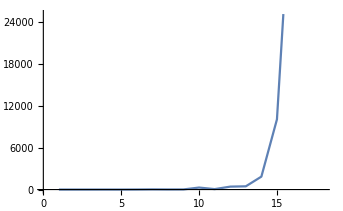

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
Partition[Flatten[Map[Boole[Sign[#]≠-1]&,Map[npairnums,Permutations[Range[8]]],{2}]],576];
```

```mathematica
ArrayPlot[%]
```

-Graphics-

```mathematica
Boole[Sign[-1]≠-1]
```

0

```mathematica
Column[%]
```

{1,3,6}
{1,5,-6}
{2,-3,5}
{2,6,-5}
{4,-5,3}
{4,-6,-3}
{-1,2,6}
{-1,4,-6}
{3,-2,4}
{3,6,-4}
{5,-4,2}
{5,-6,-2}
{-2,1,5}
{-2,4,-5}
{-3,-1,4}
{-3,5,-4}
{6,-4,1}
{6,-5,-1}
{-4,1,3}
{-4,2,-3}
{-5,-1,2}
{-5,3,-2}
{-6,-2,1}
{-6,-3,-1}

```mathematica
{1,a},{a,2}
{1,a},{a,b},{b,2}
{1,a},{a,b},{b,c},{c,2}
{1,a},{a,b},{b,c},{c,d},{d,2}
```

```mathematica
FullSimplify[(a x (1-b))-((1-a)x(b))]
```

(a-b) x

```mathematica
∑_(i=1)^(m-1) ∑_(j=i+1)^m (Subscript[a, i]-Subscript[b, j]) Subscript[x, i,j]>0
```

∑_(i=1)^(-1+m) ∑_(j=1+i)^m (a_i-b_j) x_(i,j)>0

```mathematica
Map[First,Select[Table[{i,npair[i]},{i,1,100}],¬IntersectingQ[Last[#],{1,2}]&]]
```

{6,9,10,13,14,15,18,19,20,21,24,25,26,27,28,31,32,33,34,35,36,39,40,41,42,43,44,45,48,49,50,51,52,53,54,55,58,59,60,61,62,63,64,65,66,69,70,71,72,73,74,75,76,77,78,81,82,83,84,85,86,87,88,89,90,91,94,95,96,97,98,99,100}

```mathematica
Differences[%]
```

{3,1,3,1,1,3,1,1,1,3,1,1,1,1,3,1,1,1,1,1,3,1,1,1,1,1,1,3,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1}

```mathematica
Position[%,3]
```

{{1},{3},{6},{10},{15},{21},{28},{36},{45},{55},{66}}

```mathematica
Flatten[%]
```

{1,3,6,10,15,21,28,36,45,55,66}

```mathematica
InterpolatingPolynomial[%,p]
```

1+(2+1/2 (-2+p)) (-1+p)

```mathematica
FullSimplify[%]
```

```mathematica
Reduce[1/2 p (1+p)==r,p]
```

p==1/2 (-1-√(1+8 r))||p==1/2 (-1+√(1+8 r))

```mathematica
IntegerQ[1/2 (-1+√(1+8 r))]
```

```mathematica
Table[{npairnum[{1,2+npair[i][[1]]}],npairnum[{2,2+npair[i][[2]]}]},{i,1,20}]
```

```mathematica
Table[npair[i]+2,{i,1,10}]
```

{{3,4},{3,5},{4,5},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7},{6,7}}

```mathematica
x∈{a[[2]],...,b[[1]]}
```

```mathematica
{1,a}{a,2}
```

```mathematica
1,i,2
1,i,j,2
1,
```

```mathematica
a,b
a,i,b
a,i,j,b
a,i,x,j,b
```

```mathematica
1,i,2

1,3(1+5()6+5()7+6()7+5()8+6()8)4,2
1,3(1+4()6+4()7+6()7+4()8+6()8)5,2
1,4(1+3()6+6()7+6()8+7()8+6()9)5,2
1,3(1+4()5+4()7+5()7+4()8+5()8)6,2
1,4(1+5()7+5()8+7()8+5()9+7()9)6,2
```

```mathematica
"supp 1->2";
([2,3]-[1,3])+([2,4]-[1,4])+([2,5]-[1,5])
+([2,3]-[1,4])((1-[3,4])+(1-[3,5])([4,5]+4()5)+(1-[3,6])([4,6]+4()6)+)
+([2,3]-[1,5])()
+([2,4]-[1,5])()
```

```mathematica
FullSimplify[(1-a)x b-a x(1-b)]
```

(-a+b) x